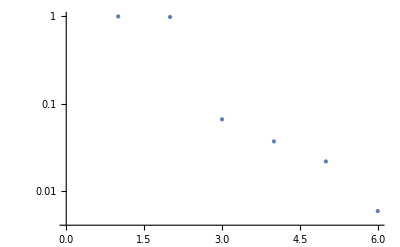

```mathematica
rnorms1=RandomVariate[NormalDistribution[0,1],100000];
rnorms2=RandomVariate[NormalDistribution[0,1],100000];
Deno[x_,p_]:= Exp[ⅈ p x]
Nume[x_,p_]:=x^2 Exp[ⅈ p x]
Obs[p_]:=Abs[Mean[Nume[rnorms1,p]]/Mean[Deno[rnorms2,p]]/(1-p^2)]
ListLogPlot[{Obs[0],Obs[2],Obs[4],Obs[6],Obs[8],Obs[10]},PlotStyle->PointSize[Large]]
```